### In this notebook we will learn how to deal with matrices in Mathematica.

```mathematica
myMatrix = {{1.0, 2.0, 3.0},{4.0, 5.0, 6.0},{7.0, 8.0, 9.0}}
myOtherMatrix = {{5.0,1.0,-2.0},{0.0,6.0,-2.0},{ⅈ,ⅇ,π}}
```

{{1.,2.,3.},{4.,5.,6.},{7.,8.,9.}}

{{5.,1.,-2.},{0.,6.,-2.},{ⅈ,ⅇ,π}}

```mathematica
{{1.,2.,3.},{4.,5.,6.},{7.,8.,9.}}
```

{{1.,2.,3.},{4.,5.,6.},{7.,8.,9.}}

### As seen above, a matrix is just a table of tables (as may be familiar from other coding languages). We can force a more conventional form for print outs:

```mathematica
myMatrix//MatrixForm
myOtherMatrix//MatrixForm
```

(1. | 2. | 3.
4. | 5. | 6.
7. | 8. | 9.)

(5. | 1. | -2.
0. | 6. | -2.
ⅈ | ⅇ | π)

### Simple arithmetic works...

```mathematica
2*myMatrix //MatrixForm
myMatrix+myOtherMatrix//MatrixForm
```

(2. | 4. | 6.
8. | 10. | 12.
14. | 16. | 18.)

(6. | 3. | 1.
4. | 11. | 4.
7.+1. ⅈ | 10.7183 | 12.1416)

### But the multiplication can be misleading. The simple * operator performs elementwise product

```mathematica
myMatrix*myOtherMatrix//MatrixForm
```

(5. | 2. | -6.
0. | 30. | -12.
0.+7. ⅈ | 21.7463 | 28.2743)

### The dot product as we know it is defined with Dot[a, b] or a simple a.b .

```mathematica
myMatrix.myOtherMatrix//MatrixForm
```

(5.+3. ⅈ | 21.1548+0. ⅈ | 3.42478+0. ⅈ
20.+6. ⅈ | 50.3097+0. ⅈ | 0.849556+0. ⅈ
35.+9. ⅈ | 79.4645+0. ⅈ | -1.72567+0. ⅈ)

### Let’s make a neat example. First let’s visualise a vector

```mathematica
ex={1,0};
ey={0,1};
myVector = {2,1};
```

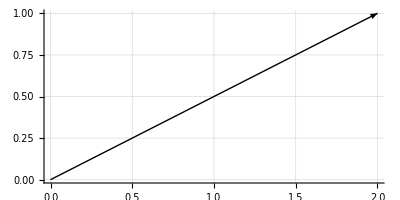

```mathematica
Graphics[{Arrow[{{0,0},myVector}]},Axes->True,GridLines->Automatic]
```

### Let’s write a matrix that swaps x and y

```mathematica
swapMatrix = {{0,1},{1,0}};
swapMatrix//MatrixForm
```

(0 | 1
1 | 0)

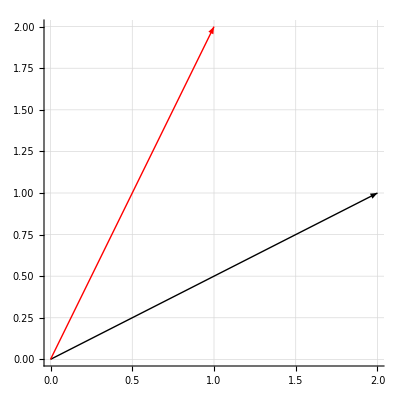

```mathematica
Graphics[{Arrow[{{0,0},myVector}],Red,Arrow[{{0,0},swapMatrix.myVector}]},Axes->True,GridLines->Automatic]
```

### Now it is your turn. Use the built in functions to find the Eigenvectors and Eigenvalues of the matrix below

```mathematica
myNewMatrix={{2.0, -1.0},{-1.0, 3.0}};
myNewMatrix//MatrixForm
```

(2. | -1.
-1. | 3.)

```mathematica
eigenVecs=Eigenvectors[myNewMatrix]
eigenVals=Eigenvalues[myNewMatrix]
```

{{-0.525731,0.850651},{-0.850651,-0.525731}}

{3.61803,1.38197}

### Now plot those eigenvectors. Apply the matrix to the eigenvectors and see the eigenvalues make sense

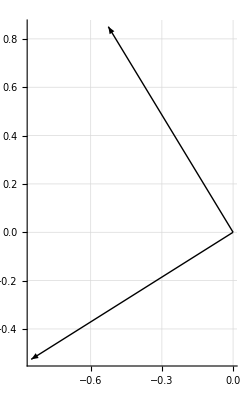

```mathematica
Graphics[{Arrow[{{0,0},eigenVecs[[1]]}],Arrow[{{0,0},eigenVecs[[2]]}]},Axes->True,GridLines->Automatic]
```

```mathematica
leftMatrix = myNewMatrix.eigenVecs[[1]]
rightMatrix = eigenVals[[1]]*eigenVecs[[1]]
leftMatrix == rightMatrix
```

{-1.90211,3.07768}

{-1.90211,3.07768}

True

### Now let’s take an arbitrary vector and express it as a sum of eigenvectors

```mathematica
myNewVector = {-1.0, 2.0};
swapMatrix = {{0,1},{1,0}};
swapMatrix//MatrixForm
```

(0 | 1
1 | 0)

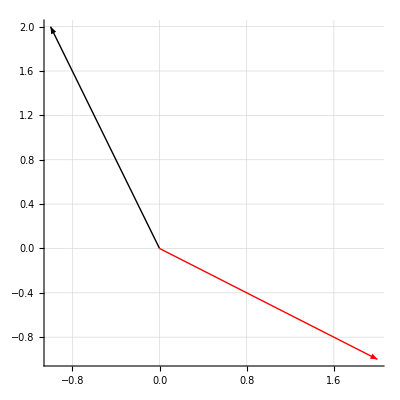

```mathematica
Graphics[{Arrow[{{0,0},myNewVector}],Red,Arrow[{{0,0},swapMatrix.myNewVector}]},Axes->True,GridLines->Automatic]
```

### We see that this vector changes direction under this matrix multiplication, and so is definitely not an eigenvector itself

```mathematica
coeffs=Solve[myNewVector==a*eigenVecs[[1]]+b*eigenVecs[[2]]]
myNewVector//MatrixForm
a*eigenVecs[[1]]+b*eigenVecs[[2]]/.coeffs//MatrixForm
```

{{a→2.22703,b→-0.200811}}

(-1.
2.)

(-1. | 2.)

### The important realisation here is that by understanding the decomposition of any vector into eigenvectors, we can understand the effect of the matrix on it. Stated another way, eigenvalues and eigenvectors contain all necessary information about the matrix. Try finding the result of matrix on vector above by using its eigen decomposition

```mathematica
newVector=coeffs[[1,1,2]]*eigenVals[[1]]*eigenVecs[[1]]+coeffs[[1,2,2]]*eigenVals[[2]]*eigenVecs[[2]]
directResult=myNewMatrix.myNewVector;
newVector ==directResult
```

{-4.,7.}

True